### Start choosing the example:

```mathematica
t=8;
beta = 0;
A = 0.2;
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/Examples/ExamplesParameters.m"];
g[x]
```

Log[x]

```mathematica
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/MFGraphs.m"];
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3,4},Adjacency Matrix→{{0,1,0,0},{0,0,1,1},{0,0,0,0},{0,0,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{3,U1},{4,U2}},Switching Costs→{{1,2,3,S1},{1,2,4,S2},{3,2,1,S3},{3,2,4,S4},{4,2,1,S5},{4,2,3,S6}}|>

```mathematica
MFGEquations=DataToEquations[Data/.{I1->1,U1->(*at vertex 3*)0,U2->(*at vertex 4*)31(*, S1->1,S2->2,S3->1,S4->1,S5->2,S6->1*),S1->(*S124*)1,S2->(*S123*)0,S3->0,S4->0,S5->0,S6->0}];//Timing
Print["current: ", MFGEquations["jvars"]/.MFGEquations["criticalreduced1"][[2]]//KeySort]
Print["transition: ", MFGEquations["jtvars"]/.MFGEquations["criticalreduced1"][[2]]//KeySort]
Print["value: ", MFGEquations["uvars"]/.MFGEquations["criticalreduced1"][[2]]//KeySort]
```

The switching costs are incompatible. 
Stopping!

Throw::nocatch: Uncaught Throw[Null] returned to top level.

Hold[Throw[Null]]

current: <|{1,1->2}→0,{1,en107->1}→1,{2,1->2}→1,{2,2->3}→0,{2,2->4}→0,{3,2->3}→1-j112,{3,3->ex108}→0,{4,2->4}→j112,{4,4->ex109}→0,{en107,en107->1}→0,{ex108,3->ex108}→1-j112,{ex109,4->ex109}→j112|>

transition: <|{1,1->2,en107->1}→0,{1,en107->1,1->2}→1,{2,1->2,2->3}→1-jt125,{2,1->2,2->4}→jt125,{2,2->3,1->2}→-j112+jt125,{2,2->3,2->4}→j112-jt125,{2,2->4,1->2}→j112-jt125,{2,2->4,2->3}→-j112+jt125,{3,2->3,3->ex108}→1-j112,{3,3->ex108,2->3}→0,{4,2->4,4->ex109}→j112,{4,4->ex109,2->4}→0|>

value: <|{1,1->2}→u134,{1,en107->1}→u134,{2,1->2}→-1+u134,{2,2->3}→u135,{2,2->4}→u136,{3,2->3}→-1+j112+u135,{3,3->ex108}→0,{4,2->4}→-j112+u136,{4,4->ex109}→31,{en107,en107->1}→u134,{ex108,3->ex108}→0,{ex109,4->ex109}→31|>

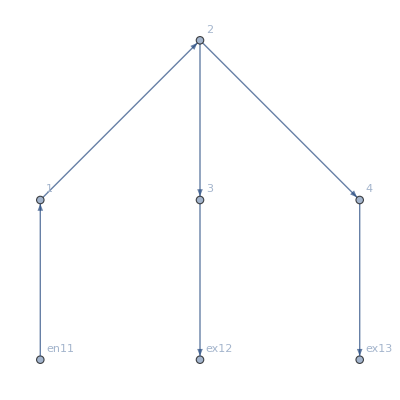

```mathematica
MFGEquations["FG"]
```

```mathematica
MFGEquations["jvars"]
MFGEquations["jtvars"]
MFGEquations["uvars"]
```

<|{2,1->2}→j14,{3,2->3}→j15,{4,2->4}→j16,{ex12,3->ex12}→j17,{ex13,4->ex13}→j18,{1,en11->1}→j19,{1,1->2}→j20,{2,2->3}→j21,{2,2->4}→j22,{3,3->ex12}→j23,{4,4->ex13}→j24,{en11,en11->1}→j25|>

<|{1,1->2,en11->1}→jt26,{1,en11->1,1->2}→jt27,{2,1->2,2->3}→jt28,{2,1->2,2->4}→jt29,{2,2->3,1->2}→jt30,{2,2->3,2->4}→jt31,{2,2->4,1->2}→jt32,{2,2->4,2->3}→jt33,{3,2->3,3->ex12}→jt34,{3,3->ex12,2->3}→jt35,{4,2->4,4->ex13}→jt36,{4,4->ex13,2->4}→jt37|>

<|{1,1->2}→u38,{2,2->3}→u39,{2,2->4}→u40,{3,3->ex12}→u41,{4,4->ex13}→u42,{en11,en11->1}→u43,{2,1->2}→u44,{3,2->3}→u45,{4,2->4}→u46,{ex12,3->ex12}→u47,{ex13,4->ex13}→u48,{1,en11->1}→u49|>

```mathematica
Select[Select[MFGEquations["EqAllAll"],(Head[#]=!= NonNegative &)],(Head[#]=!= Or &)]//Reduce
 Select[Select[MFGEquations["EqAllAll"],(Head[#]=!= NonNegative &)],(Head[#]=== Or &)]
Select[MFGEquations["EqAllAll"],(Head[#]=== NonNegative&)]//Reduce
```

jt32==-jt33+jt37&&jt31==-3-jt33+jt34+jt36&&jt30==3+jt33-jt34+jt35-jt36&&jt29==3+jt33-jt34&&jt28==-jt33+jt34&&jt27==3&&jt26==3-jt34+jt35-jt36+jt37&&j25==3-jt34+jt35-jt36+jt37&&j24==jt37&&j23==jt35&&j22==jt37&&j21==jt35&&j20==3-jt34+jt35-jt36+jt37&&j19==3&&j18==jt36&&j17==jt34&&j16==jt36&&j15==jt34&&j14==3&&u43==u49&&u47==1&&u41==1&&u48==0&&u42==0

(j20==0||j14==0)&&(j21==0||j15==0)&&(j22==0||j16==0)&&(j23==0||j17==0)&&(j24==0||j18==0)&&(j25==0||j19==0)&&(jt26==0||jt27==0)&&(jt28==0||jt30==0)&&(jt29==0||jt32==0)&&(jt31==0||jt33==0)&&(jt34==0||jt35==0)&&(jt36==0||jt37==0)&&(jt26==0||-u38+u49==0)&&(jt27==0||u38-u49==0)&&(jt28==0||S2+u39-u44==0)&&(jt29==0||2+u40-u44==0)&&(jt30==0||-u39+u44==0)&&(jt31==0||-u39+u40==0)&&(jt32==0||-u40+u44==0)&&(jt33==0||u39-u40==0)&&(jt34==0||u41-u45==0)&&(jt35==0||-u41+u45==0)&&(jt36==0||u42-u46==0)&&(jt37==0||-u42+u46==0)

(u44|u45|u46|u49)∈ℝ&&j14≥0&&j15≥0&&j16≥0&&j17≥0&&j18≥0&&j19≥0&&j20≥0&&j21≥0&&j22≥0&&j23≥0&&j24≥0&&j25≥0&&jt26≥0&&jt27≥0&&jt28≥0&&jt29≥0&&jt30≥0&&jt31≥0&&jt32≥0&&jt33≥0&&jt34≥0&&jt35≥0&&jt36≥0&&jt37≥0&&u38==u49&&-2+u44≤u40≤u44&&S2≥-u40+u44&&u39==u40&&u41==u45&&u42==u46

```mathematica
DataToEquations
```

#### Non-linear case

```mathematica
alpha = 0;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 1.2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 1.5;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

```mathematica
alpha = 1.6;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,
SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 1.8;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 1.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```